```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY190/sec_int_data/675nm.dat"]
```

{{1.16196,0.247016},{1.1485,0.235704},{1.13288,0.235704},{1.11879,0.200161},{1.10986,0.146176},{1.10188,0.0998453},{1.0953,0.0732505},{1.09118,0.0670042},{1.08898,0.10517},{1.08844,0.165769},{1.08969,0.198195},{1.094,0.230477},{1.09832,0.24326},{1.10319,0.250058},{1.11502,0.24998},{1.13408,0.26198},{1.14571,0.249513},{1.16039,0.252858},{1.17699,0.2599},{1.19764,0.256037},{1.21871,0.241141},{1.24216,0.24514},{1.26543,0.249357},{1.29691,0.244514},{1.32536,0.235072},{1.37118,0.231588},{1.45421,0.215837}}

-0.0595304+0.230755 x

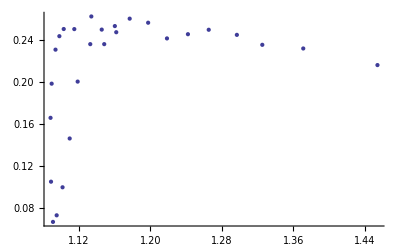

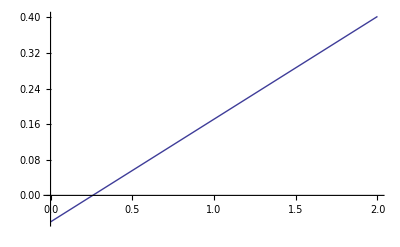

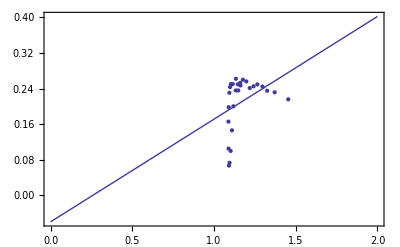

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```